```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/ignition/cantera/ratematrix

data/test

{1500,1,21,298,27.6216}

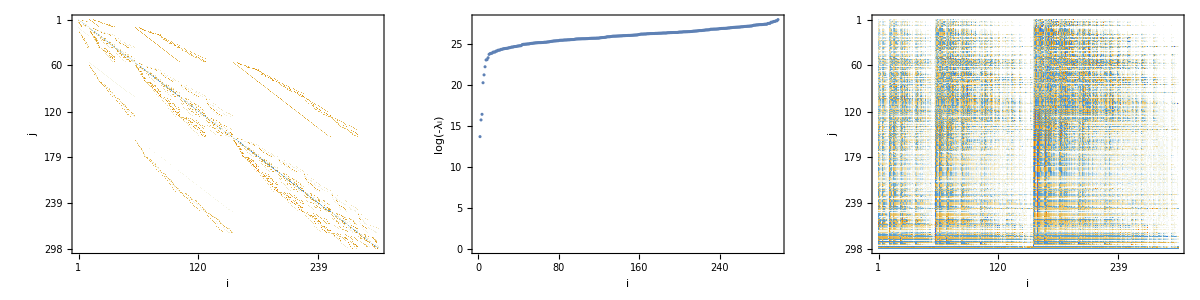

plots/example.pdf

```mathematica
filebase="data/test"
dat=Import[filebase<>"out.dat"];
{temp,press, atoms, dim,runtime} = dat[[-1,1;;5]]
file=OpenRead[filebase<>"ratematrix.npy","BinaryFormat"->True];
A=Transpose[Partition[BinaryReadList[file,"Real64"][[17;;-1]],dim]];
Close[file];
file=OpenRead[filebase<>"eigenvalues.npy","BinaryFormat"->True];
evals=BinaryReadList[file,"Real64"][[17;;-1]];
Close[file];
file=OpenRead[filebase<>"eigenvectors.npy","BinaryFormat"->True];
evecs=Transpose[Partition[BinaryReadList[file,"Real64"][[17;;-1]],dim]];
Close[file];
p=Grid[{{MatrixPlot[A,ImageSize->300,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{55,10},{55,55}}],ListPlot[Sort[Log[-evals]],PlotRange->All,AspectRatio->1,Axes->False,Frame->True,ImageSize->300,FrameTicks->{Automatic,Automatic},FrameLabel->{{Log[-Subscript[λ,i]],None},{i,Eigenvalues}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{55,10},{55,55}}],MatrixPlot[SortBy[Transpose[{evecs,evals}],#[[2]]&][[All,1]],ImageSize->300,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{55,10},{55,55}}]}}]
Export["plots/example.pdf",p]
```

## Runtimes

{{9,19,0.0115093,332,9},{12,48,0.0813439,1225,12},{15,89,0.596218,3588,15},{18,177,4.28785,9583,18},{21,298,24.6733,22616,21},{24,516,133.293,50049,24},{27,807,644.169,102480,27}}

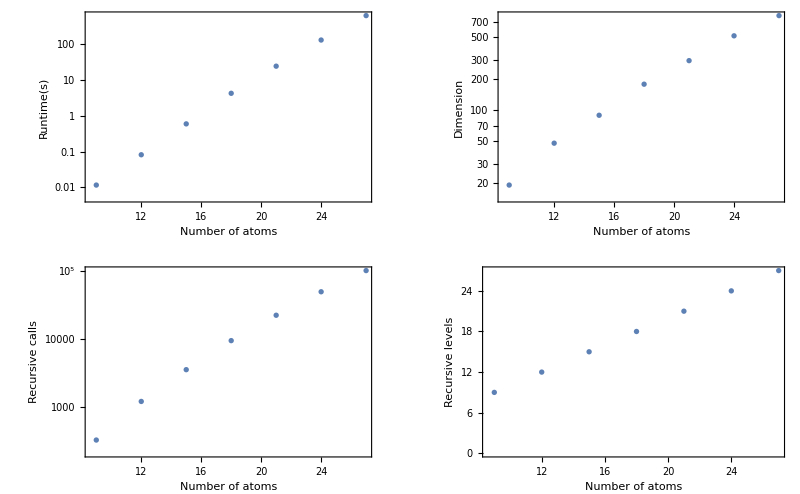

plots/logplot.pdf

```mathematica
dat=Import["data/runtimesout.dat"]
p=GraphicsGrid[{{ListLogPlot[{#[[1]],#[[2]]}&/@dat[[All,{1,3}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]],ListLogPlot[{#[[1]],#[[2]]}&/@dat[[All,{1,2}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]]},{ListLogPlot[{#[[1]],#[[2]]}&/@dat[[All,{1,4}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive calls"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]],ListPlot[{#[[1]],#[[2]]}&/@dat[[All,{1,5}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive levels"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]]}}]
Export["plots/runtimes.pdf",p]
```

## Temperature - pressure sweep

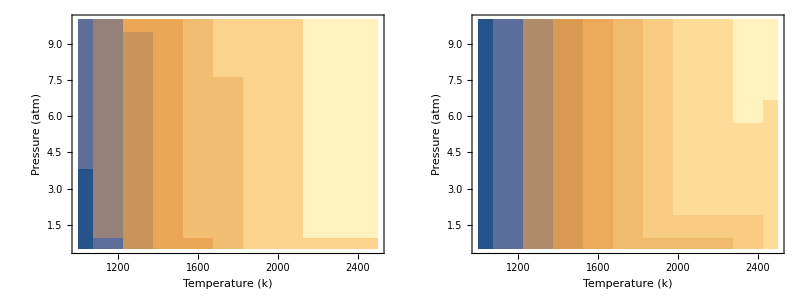

plots/sweep.pdf

```mathematica
sweep=Import["data/sweepout.dat"];
p=Grid[{{ListContourPlot[{#[[1]],#[[2]],Log[-#[[-2]]]}&/@sweep,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Pressure (atm)",None},{"Temperature (k)",Log[-Subscript[λ,1]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0],ListContourPlot[{#[[1]],#[[2]],Log[-#[[-3]]]}&/@sweep,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Pressure (atm)",None},{"Temperature (k)",Log[-Subscript[λ,2]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0]}}]
Export["plots/sweep.pdf",p]
```

## Temperature - atoms sweep

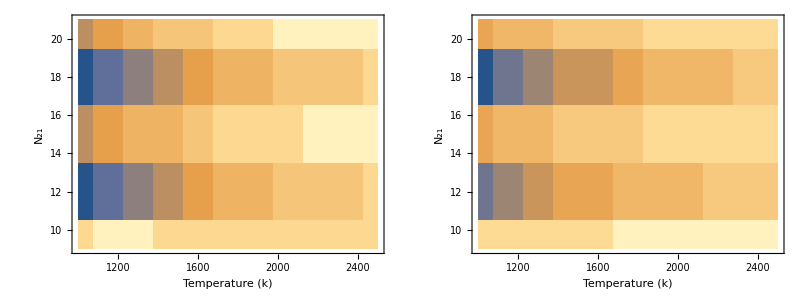

plots/sweep2.pdf

```mathematica
sweep2=Import["data/sweep2out.dat"];
p=Grid[{{ListContourPlot[{#[[1]],#[[3]],Log[-#[[-2]]]}&/@sweep2,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,atoms],None},{"Temperature (k)",Log[-Subscript[λ,1]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0,PlotRange->All],ListContourPlot[{#[[1]],#[[3]],Log[-#[[-3]]]}&/@sweep2,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,atoms],None},{"Temperature (k)",Log[-Subscript[λ,2]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0,PlotRange->All]}}]
Export["plots/sweep2.pdf",p]
```